Cavity Methods for QP

## Solve self-consistent equations for the cavity method

```mathematica
cavity[gammainv_, mu_, sigc_, tauinv_, k_, sigk_, m_, sigm_]:=
Module[{}, 
w0[Delta_]:= CDF[NormalDistribution[],Delta];
w1[Delta_]:=Delta+PDF[NormalDistribution[],-Delta]-Delta*CDF[NormalDistribution[],-Delta];
w2[Delta_]:=(Delta^2+1)*(1-CDF[NormalDistribution[],-Delta])+Delta*PDF[NormalDistribution[],-Delta];

eta[Delg_,DelK_]:=w0[DelK]-(gammainv)*w0[Delg];
d[Delg_,DelK_]:=w0[DelK]^2-w2[DelK]*w2[Delg]*gammainv;
nR[Delg_,DelK_]:=sigk^2*sigc^2*eta[Delg,DelK]^2+sigm^2*w2[Delg]*gammainv;
nN[Delg_,DelK_]:=w0[DelK]^2*sigm^2+sigc^2*sigk^2*eta[Delg,DelK]^2*w2[DelK];


r[Delg_,DelK_]:=w1[DelK]*Sqrt[nR[Delg,DelK]/d[Delg,DelK]]/sigc;
n[Delg_,DelK_]:=w1[Delg]*Sqrt[nN[Delg,DelK]/d[Delg,DelK]]/(sigc^2*eta[Delg,DelK]);
qR[Delg_,DelK_]:=w2[DelK]*nR[Delg,DelK]/(sigc^2 * d[Delg,DelK]);
qN[Delg_,DelK_]:=w2[Delg]*nN[Delg,DelK]/(sigc^4 *eta[Delg,DelK]^2 * d[Delg,DelK]);

kR[Delg_,DelK_]:=k*r[Delg,DelK]+sigk^2*w0[DelK]/w0[DelK]*(w0[DelK]-gammainv*w0[Delg]);
err[Delg_,DelK_]:=Abs[(DelK*w0[DelK]*sigc*Sqrt[nR[Delg,DelK]]-k*sigc^2*eta[Delg,DelK]*Sqrt[d[Delg,DelK]]+mu*w1[Delg]*Sqrt[nN[Delg,DelK]]*gammainv)]^2+
Abs[(Delg*sigc*Sqrt[nN[Delg,DelK]]-mu*w1[DelK]*Sqrt[nR[Delg,DelK]]+m*sigc*Sqrt[d[Delg,DelK]])]^2;
sols=NMinimize[{err[Delg,DelK],{eta[Delg,DelK]>0,Delg>-5}},{{Delg,-3,3},{DelK,-3,3}},Method->"RandomSearch"];
Sol=Flatten[Append[sols[[2]],errval->sols[[1]]]];
output={w0[Delg],n[Delg,DelK],qN[Delg,DelK],w0[DelK],r[Delg,DelK],qR[Delg,DelK],gammainv, mu, sigc, tauinv, k, sigk, m, sigm,errval,k^2+sigk^2+qR[Delg,DelK]-2*kR[Delg,DelK],kR[Delg,DelK]}/.Sol ]
```

```mathematica
gammainv = 1.0;
sigc = 0.1;
mu = 1.;
tauinv = 1.;
k = 1.0;
m = 1.0;
sigm = 0.1;
sigk=1.0;
cavity[gammainv, mu, sigc, tauinv, k, sigk, m, sigm]
```

{0.0430958,0.374089,5.83575,0.728542,0.749925,1.12416,1.,1.,0.1,1.,1.,1.,1.,0.1,2.99295×10^-19,0.253412,1.43537}

### Find current directory and files

```mathematica
Module[{directory=SystemDialogInput["Directory"]},If[directory=!=$Canceled,SetDirectory[directory]]];
```

### Load the results of cavity solutions

```mathematica
datacL1=Table[cavity[x, mu,1.0, tauinv, k, sigk, m, sigm],{x,0.1,11.1,1.}];
datacL2=Table[cavity[x, mu,0.5, tauinv, k, sigk, m, sigm],{x,0.1,11.1,1.}];
datacL3=Table[cavity[x, mu,0.1, tauinv, k, sigk, m, sigm],{x,0.1,11.1,1.}];
datacL1=Prepend[datacL1,{"mean_phiN","mean_N","q_N", "mean_phiR", "mean_R", "q_R", "gammainv", "mu", "sigc", "tauinv", "k","sigk", "m", "sigm", "error", "opf", "kr"}];
datacL2=Prepend[datacL2,{"mean_phiN","mean_N","q_N", "mean_phiR", "mean_R", "q_R", "gammainv", "mu", "sigc", "tauinv", "k","sigk", "m", "sigm", "error", "opf", "kr"}];
datacL3=Prepend[datacL3,{"mean_phiN","mean_N","q_N", "mean_phiR", "mean_R", "q_R", "gammainv", "mu", "sigc", "tauinv", "k","sigk", "m", "sigm", "error", "opf", "kr"}];
```

```mathematica
Export["/Users/wenpingcui/Downloads/Cavity_sigc1.0.csv",datacL1,"CSV"];
Export["/Users/wenpingcui/Downloads/Cavity_sigc0.5.csv",datacL2,"CSV"];
Export["/Users/wenpingcui/Downloads/Cavity_sigc0.1.csv",datacL3,"CSV"];
```

```mathematica
datacL3=Import["/home/cuiw/Dropbox/RandomQP/Cavity/Data/Cavity_sigc0.1.csv","Data"];
datacL2=Import["/home/cuiw/Dropbox/RandomQP/Cavity/Data/Cavity_sigc0.5.csv","Data"];
datacL1=Import["/home/cuiw/Dropbox/RandomQP/Cavity/Data/Cavity_sigc1.0.csv","Data"];
```

### Load the results of MCRM simulations

```mathematica
datacsL3=Import["/home/cuiw/Dropbox/RandomQP/Cavity/Data/MCRM_sigc0.1.csv","Data"];
datacsL2=Import["/home/cuiw/Dropbox/RandomQP/Cavity/Data/MCRM_sigc0.5.csv","Data"];
datacsL1=Import["/home/cuiw/Dropbox/RandomQP/Cavity/Data/MCRM_sigc1.0.csv","Data"];
```

### Load the results of random quadratic programming

```mathematica
datac1L3=Import["/home/cuiw/Dropbox/RandomQP/Cavity/Data/RQP_sigc0.1.csv","Data"];
datac1L2=Import["/home/cuiw/Dropbox/RandomQP/Cavity/Data/RQP_sigc0.5.csv","Data"];
datac1L1=Import["/home/cuiw/Dropbox/RandomQP/Cavity/Data/RQP_sigc1.0.csv","Data"];
```

### Fit the data

```mathematica
Needs["ErrorBarPlots`"]
phir1=Interpolation[datacL1[[2;;,{7,4}]]];
phir2=Interpolation[datacL2[[2;;,{7,4}]]];
phir3=Interpolation[datacL3[[2;;,{7,4}]]];
phin1=Interpolation[datacL1[[2;;,{7,1}]]];
phin2=Interpolation[datacL2[[2;;,{7,1}]]];
phin3=Interpolation[datacL3[[2;;,{7,1}]]];
fopt1=Interpolation[datacL1[[2;;,{7,16}]]];
fopt2=Interpolation[datacL2[[2;;,{7,16}]]];
fopt3=Interpolation[datacL3[[2;;,{7,16}]]];

phirs1=Interpolation[datacsL1[[2;;,{16,2}]]];
phirs2=Interpolation[datacsL2[[2;;,{16,2}]]];
phirs3=Interpolation[datacsL3[[2;;,{16,2}]]];
phins1=Interpolation[datacsL1[[2;;,{16,1}]]];
phins2=Interpolation[datacsL2[[2;;,{16,1}]]];
phins3=Interpolation[datacsL3[[2;;,{16,1}]]];
foptsi1=Interpolation[datacsL1[[2;;,{16,26}]]];
foptsi2=Interpolation[datacsL2[[2;;,{16,26}]]];
foptsi3=Interpolation[datacsL3[[2;;,{16,26}]]];

phircs1=Interpolation[datac1L1[[2;;,{16,2}]]];
phircse1={{#16,#2},ErrorBar[#23]}&@@@datac1L1;
phircs2=Interpolation[datac1L2[[2;;,{16,2}]]];
phircse2={{#16,#2},ErrorBar[#23]}&@@@datac1L2;
phircs3=Interpolation[datac1L3[[2;;,{16,2}]]];
phircse3={{#16,#2},ErrorBar[#23]}&@@@datac1L3;
phincs1=Interpolation[datac1L1[[2;;,{16,1}]]];
phincse1={{#16,#1},ErrorBar[#22]}&@@@datac1L1;
phincs2=Interpolation[datac1L2[[2;;,{16,1}]]];
phincse2={{#16,#1},ErrorBar[#22]}&@@@datac1L2;
phincs3=Interpolation[datac1L3[[2;;,{16,1}]]];
phincse3={{#16,#1},ErrorBar[#22]}&@@@datac1L3;
fopts1=Interpolation[datac1L1[[2;;,{16,26}]]];
foptse1={{#16,#26},ErrorBar[#27]}&@@@datac1L1;
fopts2=Interpolation[datac1L2[[2;;,{16,26}]]];
foptse2={{#16,#26},ErrorBar[#27]}&@@@datac1L2;
fopts3=Interpolation[datac1L3[[2;;,{16,26}]]];
foptse3={{#16,#26},ErrorBar[#27]}&@@@datac1L3;
```

## Plot for FIG. 2: Random Quadratic Programming (RQP)

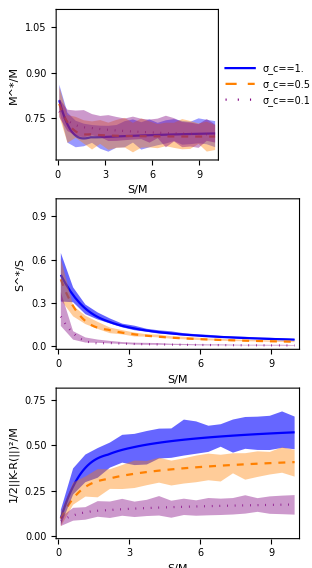

```mathematica
p1=Plot[{phir1[x],phir2[x],phir3[x]},{x,0.1,10.0},PlotLegends->Placed[{Style[ToExpression["\\sigma_c=1.0",TeXForm]],Style[ToExpression["\\sigma_c=0.5",TeXForm]],Style[ToExpression["\\sigma_c=0.1",TeXForm]]},{0.6,0.7}],Frame->True,FrameLabel->{"S/M","M^*/M"},ImagePadding->{{68,20},{40,10}},ImageSize->300,PlotRange->{{0.1,10.01},{0.62,1.1}},LabelStyle->Directive[Plain,15],PlotStyle->{Blue,{Orange,Dashed},{Purple,Dotted}}];
p2=Plot[{phin1[x],phin2[x],phin3[x]},{x,0.1,10.0},Frame->True,FrameLabel->{"S/M","S^*/S"},ImagePadding->{{68,20},{40,10}},ImageSize->300,PlotRange->{{0.1,10.01},{0,1.0}},PlotStyle->{Blue,{Orange,Dashed},{Purple,Dotted}},LabelStyle->Directive[Plain,15]];

p3=Plot[{0.5*fopt1[x],0.5*fopt2[x],0.5*fopt3[x]},{x,0.1,10.0},Frame->True,FrameLabel->{"S/M","1/2||K-R(||)^2/M"},ImagePadding->{{68,20},{40,10}},ImageSize->300,PlotRange->{{0.1,10.01},{0,0.8}},PlotStyle->{Blue,{Orange,Dashed},{Purple,Dotted}},LabelStyle->Directive[Plain,15]];
phir1plus={#16,#2+#23}&@@@datac1L1;
phir1minus={#16,#2-#23}&@@@datac1L1;
p11=ListLinePlot[{phir1plus,phir1minus},PlotStyle->{Opacity[0],Opacity[0]},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.4],Blue],PlotRange->All];

phir1plus={#16,#2+#23}&@@@datac1L2;
phir1minus={#16,#2-#23}&@@@datac1L2;
p12=ListLinePlot[{phir1plus,phir1minus},PlotStyle->{Opacity[0],Opacity[0]},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.4],Orange],PlotRange->All];

phir1plus={#16,#2+#23}&@@@datac1L3;
phir1minus={#16,#2-#23}&@@@datac1L3;
p13=ListLinePlot[{phir1plus,phir1minus},PlotStyle->{Opacity[0],Opacity[0]},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.4],Purple],PlotRange->All];
p1=Show[{p1,p11,p12,p13}];

phir1plus={#16,#1+#22}&@@@datac1L1;
phir1minus={#16,#1-#22}&@@@datac1L1;
p21=ListLinePlot[{phir1plus,phir1minus},PlotStyle->{Opacity[0],Opacity[0]},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.6],Blue],PlotRange->All];

phir1plus={#16,#1+#22}&@@@datac1L2;
phir1minus={#16,#1-#22}&@@@datac1L2;
p22=ListLinePlot[{phir1plus,phir1minus},PlotStyle->{Opacity[0],Opacity[0]},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.4],Orange],PlotRange->All];

phir1plus={#16,#1+#22}&@@@datac1L3;
phir1minus={#16,#1-#22}&@@@datac1L3;
p23=ListLinePlot[{phir1plus,phir1minus},PlotStyle->{Opacity[0],Opacity[0]},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.4],Purple],PlotRange->All];
p2=Show[{p2,p21,p22,p23}];


phir1plus={#16,0.5*#26+0.5*#27}&@@@datac1L1;
phir1minus={#16,0.5*#26-0.5*#27}&@@@datac1L1;
p31=ListLinePlot[{phir1plus,phir1minus},PlotStyle->{Opacity[0],Opacity[0]},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.6],Blue],PlotRange->All];

phir1plus={#16,0.5*#26+0.5*#27}&@@@datac1L2;
phir1minus={#16,0.5*#26-0.5*#27}&@@@datac1L2;
p32=ListLinePlot[{phir1plus,phir1minus},PlotStyle->{Opacity[0],Opacity[0]},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.4],Orange],PlotRange->All];

phir1plus={#16,0.5*#26+0.5*#27}&@@@datac1L3;
phir1minus={#16,0.5*#26-0.5*#27}&@@@datac1L3;
p33=ListLinePlot[{phir1plus,phir1minus},PlotStyle->{Opacity[0],Opacity[0]},Filling->{1->{2}},FillingStyle->Directive[Opacity[0.4],Purple],PlotRange->All,LabelStyle->Directive[Black,15]];
p3=Show[{p3,p31,p32,p33}];
GraphicsGrid[{{p1}, {p2},{p3}},Spacings->Scaled[.0]]
```

```mathematica
Export["/home/cuiw/Downloads/Cavity_QP_f1.pdf",%83,"PDF"]
```

/home/cuiw/Downloads/Cavity_QP_f1.pdf

## Plot for FIG. 3: Comparison of Cavity Solution, RQP, and dual MCRMs

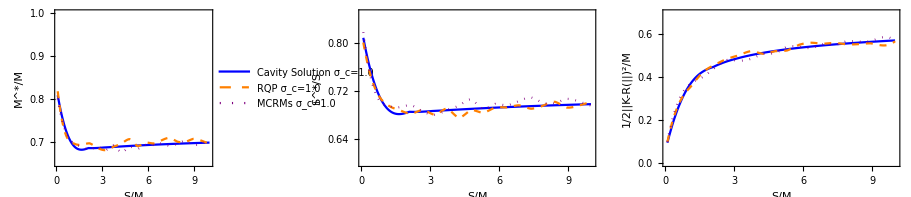

```mathematica
p1=Plot[{phir1[x],phircs1[x],phirs1[x]},{x,0.1,10.0},PlotStyle->{{Blue},{Orange,Dashed},{Purple,Dotted}},PlotLegends->Placed[{ "Cavity Solution σ_c=1.0","RQP σ_c=1.0","MCRMs σ_c=1.0"},{0.5,0.7}],Frame->True,FrameLabel->{"S/M","M^*/M"},ImagePadding->{{70,20},{40,10}},LabelStyle->Directive[Plain,14]
,ImageSize->300,PlotRange->{{0.1,10.01},{0.65,1.0}}];
p2=Plot[{phir1[x],phirs1[x],phircs1[x]},{x,0.1,10.0},Frame->True,FrameLabel->{"S/M","S^*/S"},ImagePadding->{{70,20},{40,10}},ImageSize->300,LabelStyle->Directive[Plain,14],PlotRange->{{0.1,10.01},{0.6,0.85}},PlotStyle->{{Blue},{Orange,Dashed},{Purple,Dotted}}];



p3=Plot[{0.5*fopt1[x],0.5*foptsi1[x],0.5*fopts1[x]},{x,0.1,10.0},Frame->True,FrameLabel->{"S/M","1/2||K-R(||)^2/M"},ImagePadding->{{70,20},{40,10}},ImageSize->300,PlotRange->{{0.1,10.01},{0,0.7}},LabelStyle->Directive[Plain,14],PlotStyle->{{Blue},{Orange,Dashed},{Purple,Dotted}}];
GraphicsGrid[{{p1, p2,p3}},Spacings->Scaled[.001]]
```

```mathematica
Export["/home/cuiw/Downloads/Cavity_QP_f2.pdf",%107,"PDF"]
```

/home/cuiw/Downloads/Cavity_QP_f2.pdf